```mathematica
QCircle =ParametricPlot[{Sin[a],Cos[a]},{a,0,Pi/2},PlotStyle->{Dashed,Lighter@Gray}];
```

```mathematica
QCirclep =ParametricPlot[{Sin[a],Cos[a]},{a,Pi/2-ArcCos[Gl2⟦1,1⟧],Pi/2},PlotStyle->{Orange,Thickness[.03],Opacity[.8]}];
```

```mathematica
Arrows2D=Graphics[
{Gray,Arrowheads[0.05],
Arrow[{{0,0},{1.15,0}},.008],
Arrow[{{0,0},{0,1.15}},.008],
Text[Style["ρ",Darker@Gray,17],{1.2,0}],Text[Style["μ",Darker@Gray,17],{0,1.2}]
}];
```

```mathematica
c1=.65;
A2={{.3, c1},{.8*c1, 0}};
At2=Transpose@A2;
AN2 = Transpose[Table[Normalize[At2⟦i⟧],{i,2}]];
Gl2 = Transpose@AN2;
```

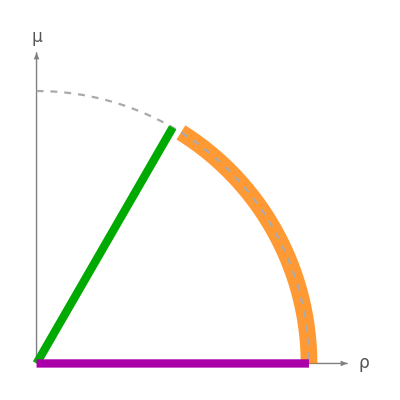

```mathematica
a2=Show[
Arrows2D,
QCirclep,QCircle,
ListLinePlot[{{0,0},{Gl2⟦1,1⟧,Gl2⟦1,2⟧}}, PlotStyle->{Darker@Green,Directive[Thickness[.015]]}],
ListLinePlot[{{0,0},{1,0}}, PlotStyle->{Darker@Magenta,Directive[Thickness[.015]]}]
]
```

```mathematica
c2=.31;
A={{.52, 0, c1},{0,.48,c2},{.8*c1, .8*c2, 0}};
{{0.52,0,0.65},{0,0.48,0.31},{0.52,0.248,0}};
At=Transpose@A;
AN = Transpose[Table[Normalize[At⟦i⟧],{i,3}]];
Gl=Transpose@AN;
Glm = -Gl;
```

```mathematica
axesLogi=Graphics3D[{Gray,Arrowheads[0.02],
Arrow[Tube[{{0,0,0},-{1.15,0,0}},.003]],
Arrow[Tube[{{0,0,0},-{0,1.15,0}},.003]],
Tube[{{0,0,0},-{-1,0,0}},.003],
Tube[{{0,0,0},-{0,-1,0}},.003],
Tube[{{0,0,0},-{0,0,-1}},.003],
Arrow[Tube[{{0,0,0},-{0,0,1.15}},.003]],
Text[Style[Subscript["ρ",1],Darker@Gray,15],-{1.2,.1,0.0}],
Text[Style[Subscript["ρ",2],Darker@Gray,15],-{0,1.29,0}],
Text[Style["μ",Darker@Gray,15],-{0,0,1.22}]},Boxed->False];
```

```mathematica
circle3Df[centre_:{0,0,0},radius_:1,normal_:{0,0,1},angle_:{0,2 Pi}]:=Composition[Line,Map[RotationTransform[{{0,0,1},normal},centre],#]&,Map[Append[#,Last@centre]&,#]&,Append[DeleteDuplicates[Most@#],Last@#]&,Level[#,{-2}]&,MeshPrimitives[#,1]&,DiscretizeRegion,If][First@Differences@angle>=2 Pi,Circle[Most@centre,radius],Circle[Most@centre,radius,angle]]
```

```mathematica
circle3Di[centre_:{0,0,0},radius_:1,normal_:{0,0,1},angle_:{0,Pi/2}]:=Composition[Line,Map[RotationTransform[{{0,0,1},normal},centre],#]&,Map[Append[#,Last@centre]&,#]&,Append[DeleteDuplicates[Most@#],Last@#]&,Level[#,{-2}]&,MeshPrimitives[#,1]&,DiscretizeRegion,If][First@Differences@angle>=2 Pi,Circle[Most@centre,radius],Circle[Most@centre,radius,angle]]
```

```mathematica
cs=Show[Graphics3D[Style[circle3Di[{0,0,0},1,{0,0,1},{-Pi,-Pi/2}],Lighting->{{"Ambient", LightRed}},Gray, Thickness[.007]],Boxed->False],
Graphics3D[Style[circle3Di[{0,0,0},1,{1,0,0},{-Pi/2,0}],Gray, Thickness[.007]]],Graphics3D[Style[circle3Di[{0,0,0},1,{0,1,0},{Pi/2,Pi}],Gray, Thickness[.007]]]];
```

```mathematica
b3=Show[Graphics3D[{(*ClipPlanes->{InfinitePlane[{{0,0,0},ax⟦1⟧,-ax⟦3⟧}],InfinitePlane[{{0,0,0},-ax⟦2⟧,ax⟦1⟧}],InfinitePlane[{-ax⟦2⟧,-ax⟦3⟧,{0,0,0}}]},Gray,Opacity[.07],Sphere[{0,0,0}],*)ClipPlanes->{InfinitePlane[{{0,0,0},-Glm⟦1⟧,Glm⟦3⟧}],InfinitePlane[{{0,0,0},Glm⟦2⟧,-Glm⟦1⟧}],InfinitePlane[{Glm⟦2⟧,Glm⟦3⟧,{0,0,0}}]},Orange,Opacity[.4],Sphere[]},Boxed->False],ListLinePlot3D[{{0,0,0},Glm⟦1⟧},PlotStyle->{Thickness[.01],Red}],
ListLinePlot3D[{{0,0,0},Glm⟦3⟧},PlotStyle->{Thickness[.01],Darker@Green}],
ListLinePlot3D[{{0,0,0},Glm⟦2⟧},PlotStyle->{Thickness[.01],Lighter@Purple}],axesLogi,Graphics3D[Style[circle3Df[],Lighting->{{"Ambient", LightRed}},Lighter@Gray, Dashed],Boxed->False],Graphics3D[Style[circle3Df[{0,0,0},1,{1,0,0}],Lighter@Gray, Dashed]],Graphics3D[Style[circle3Df[{0,0,0},1,{0,1,0}],Lighter@Gray, Dashed]],cs];
```

```mathematica
Show[b3,ViewAngle->0.9,ViewPoint->{-0.6,-Pi/2,-0.2},ViewVertical->{0.04143327189189544,0.10148772779237178,-0.9939736038184684}]
```

-Graphics3D-